Jalil Villalobos Alva

Beginning Mathematica and Wolfram for Data Science: ML & DL              < >    Ξ

Edited by Hao Feng

## Neural Networks with the Wolfram Language

This chapter starts with the basic foundations of the neural network framework in the Wolfram Language. The chapter begins with the concepts of layers, how to use the
commands for different layers, and the most common layers. You learn how to enter
data into the layers by the net port and the different forms of equivalent expression of the layers. This topic is followed by how to distinguish different layers by their symbol. You see that layers can have multiple options that enable them to have various specifications by viewing the concept of a layer in the Wolfram Language scheme, comparing different layers with different purposes, and performing different computations. You also achieve this by looking at the various activation functions supported by the Wolfram Language and inspecting the plots of each function in addition to different syntax forms. Next, you learn about encoders and decoders and how these tools are used to construct a neural network model, depending on the task to be fulfilled. You then learn how these encoders and decoders are used to convert different data types to numeric arrays and how to convert the numeric arrays back to the initial data. You introduce the concept of a container, what it means for the created models, and what types exist. You see how to handle and build containers with different commands and graphically visualize the created model. You see how the Wolfram Neural Net Framework supports MXNet-related operations and how to export a network to the format of the MXNet operation.

### Layers

It is necessary to understand that neural networks, in general and in the Wolfram
Language, are built from layers. A layer is a term that can be applied to a collection of
nodes that operate together at a specific level within the neural network. The layer is an essential and straightforward member for constructing a neural network.

#### Input Data

The data handled by the layers is of a numeric type and not of another kind. Input
variables can be vectors, a unidimensional list, matrices, a two-dimensional list, arrays,
a list of lists, or any other numeric tensor. These input variables can be either features or attributes of the dataset of study, with a known or multidimensional shape. These types of input attributes are associated with the input layer, for which the feature size, in turn, must be equal to the input size of a layer, but not every layer receives the same input and returns the same output; every input varies depending on the type of layer to be used. This definition is one of the most basic ideas in neural networks since they are a crucial component of the whole structure that involves the term neural network. A remark here is to distinguish input from input layer since they do not mean the same.

#### Linear Layer

A linear layer is the most common and widely used layer in a neural network. To build the simplest layer in the Wolfram Language, use the LinearLayer command.

```mathematica
LinearLayer["Input"->1,"Output"->2]
```

LinearLayer[…]

It represents the LinearLayer object in the Wolfram Language. Clicking the plus icon shows the internal parameters, including details about the layer port’s input and output and array rank of the weights and biases of the linear layer.

Each layer has an input port and an output port. Each port has an associated size of
what is entering the layer and what is going out. In the latter case, a vector of size one is entering, and the layer returns a vector of size two.

#### Weights and Biases

The general form of a linear layer is given by the following expression of the dot product w⋅x + b, where x is the data vector, w represents the matrix of the weights, and b is the vector of the biases. Linear layers have other associated names, like fully connected layers, as in the MXnet framework. The input of the layers in the Wolfram Language receives numerical tensors as input—that is, they only act on numerical arrays. To explicitly enter the size of input and output, you write the form of the input port and the output port followed by different options: “Input” or “Output” → {size, Options.}. Options include defining a real number (Real), a vector of form n (single number n), an array ({n1 * n2 * n3} ...), or a NetEncoder, which you see later. Following are some equivalent ways to write layers

```mathematica
LinearLayer["Input"->{2,"Real"},"Output"->{3,1}]
```

LinearLayer[…]

The layer receives a vector of size two (list of length 2),  comprised of real numbers, and the output is a matrix of the shape 3×2. When a real number is specified within the Wolfram Neural Network Framework, it works with the precision of a Real32. When no arguments are added to the layer, the input and output shapes are inferred. To manually assign the weights and biases, write “Weights” → number, “Biases” → number; None is also available for no weights or biases. This is shown in the following example, where weights and biases are set to a fixed value of 1 and 2.

```mathematica
LinearLayer["Input"->1,"Output"->1,"Weights"->1,"Biases"->2]
```

LinearLayer[…]

#### Initializing a Layer

Another command allows you to initialize the layer with random values: NetInitialize. So, to establish hold values of weights or biases, you can also use the LearningRateMultipliers option. Besides this, LearningRateMultipliers also mark the rate at which a layer learns during the training phase.

```mathematica
NetInitialize[LinearLayer["Input"->"Real","Output"->"Real",LearningRateMultipliers->{"Biases"->1}]]
```

LinearLayer[…]

When a layer is initialized, the uninitialized text disappears. If you observe the properties of the new layer, they appear within the training parameters where fixed biases have been established, and a learning rate has been set. The options for NetInitialize are Method and RandomSeeding. The available methods are Kaiming, Xavier, Orthogonal (orthogonal weights), and Random (weights selection from a distribution). For example, you can use the Xavier initialization sampling from a normal distribution.

```mathematica
NetInitialize[LinearLayer["Input"->"Real","Output"->"Real",LearningRateMultipliers->{"Biases"->1}],Method->{"Xavier","Distribution"->"Normal"},RandomSeeding->888]
```

LinearLayer[…]

Note: The Option command is recommended to see the options set for a layer.

Despite being able to establish the weights and biases manually, it is advisable to
start the layer with random values to maintain a certain level of complexity in the overall structure of a model since, on the contrary, this could have an impact on the creation of a neural network that does not make accurate predictions for non-linear behavior.

#### Retrieving Data

NetExtract retrieves the value of the weights and biases in the form NetExtract [net,
{level1, level2, ...}. The weights and bias parameters of the linear layers are packed in NumericArray objects. This object has the values, dimensions, and type of the values in the layer. NetExtract also serves to extract layers of a network with many layers. NumericArrays are used in the Wolfram Language to reduce memory consumption and computation time.

```mathematica
linearL=NetInitialize[LinearLayer[2,"Input"->1],RandomSeeding->888]
```

LinearLayer[…]

```mathematica
NetExtract[linearL,#]&/@{"Weights","Biases"}//TableForm
```

NumericArray[…]
NumericArray[…]

With Normal, you convert them to lists.

```mathematica
TableForm[SetPrecision[{{Normal[NetExtract[linearL,"Weights"]]},{Normal[NetExtract[linearL,"Biases"]]}},3],TableHeadings->{{"Weights ->","Biases ->"},None}]
```

Weights -> | -0.779
0.0435
Biases -> | 0
0

For instance, a layer can receive a length of one vector to produce an output vector
of size 2.

```mathematica
linearL[4]
```

{-3.11505,0.174007}

The layer can only be evaluated when input is introduced in the appropriate shape.

```mathematica
linearL[{88,99}]
```

LinearLayer::invindata1: Data supplied to port "Input" was a length-2 vector of real numbers, but expected a length-1 vector.

$Failed

The weights and biases are the parameters that the model must learn from, which
can be adapted based on the input data that the model receives, which is why it is
initialized randomly since if you try to extract these values without initializing, you
cannot because they have not been defined.

Layers have the property of being differentiable. It is achieved with NetPortGradient, which can represent the gradient of a net output for a port or a parameter. For example, give the derivative of the output concerning the input for a particular input value.

```mathematica
linearL[2,NetPortGradient["Input"]]
```

{-0.735261}

#### Mean Squared layer

Until now, you have seen the linear layer, which has various properties. Layers with the icon of a connected rhombus, by contrast, do not contain any learnable parameters, like MeanSquaredLossLayer, AppendLayer, SummationLayer, DotLayer, ContrastiveLossLayer, and SoftmaxLayer, among others.

```mathematica
MeanSquaredLossLayer[]
```

MeanSquaredLossLayer[…]

MeanSquaredLossLayer[] has more than one input because this layer computes the
mean squared loss, which is the following expression (1/n) ∑ (Input - (Target))^2, and has
the property that compares two numeric arrays. With the MeanSquaredLossLayer, the input/output ports’ dimensions are entered in the same form as a linear layer, and the input and target values are entered as Associations.

```mathematica
MeanSquaredLossLayer["Input"->{3,2},"Target"->{3,2}][Association["Input"->{{1,2},{2,1},{3,2}},"Target"->{{2,2},{1,1},{1,3}}]]
```

1.16667

The latter example computes a MeanSquaredLossLayer for input/output dimensions of three rows and two columns or by defining first the layer and then applying the layer to the data.

Note: use the Matrixform[{{1, 2}, {2, 1}, {3, 2}}] command to verify the matrix shape of the data.

```mathematica
lossLayer=MeanSquaredLossLayer["Input"->{3,2},"Target"->{3,2}];
```

```mathematica
lossLayer@<|"Input"->{{1,2},{2,1},{3,2}},"Target"->{{2,2},{1,1},{1,3}}|>
```

1.16667

To get more details about a layer, use the Information command.

```mathematica
Information[lossLayer]
```

Net Information

To know the layer options, use the following.

```mathematica
MeanSquaredLossLayer["Input"->"Real","Target"->"Real"]//Options
```

{BatchSize→Automatic,NetEvaluationMode→Test,RandomSeeding→Automatic,TargetDevice→CPU,WorkingPrecision→Real32}

The input port and target port options are similar to that of the linear layer with the
different forms, Input → Real, n (a form of a vector n), {n1 × n2 × n3} ... (an array of n
dimensions), Varying (a vector or varying form) or a NetEncoder, but with the exception that the input and target must have the exact dimensions.

```mathematica
{MeanSquaredLossLayer["Input"->"Varying","Target"->"Varying"],MeanSquaredLossLayer["Input"->NetEncoder["Image"],"Target"->NetEncoder["Image"]],MeanSquaredLossLayer["Input"->1,"Target"->1]}//Dataset
```

#### Activation Functions

Activation functions are a crucial part of the construction of a neural network. The role of an activation function is to return an output from an established range, given an input. In the Wolfram Language, activation functions are treated as layers. The layer that is frequently used for activation function definition in the Wolfram Language neural net framework is the ElementwiseLayer. With this layer, you can represent layers that can apply a unary function to the input data elements—in other words, a function that receives only one argument. These functions are also known as activation functions. For example, one of the most common functions used is the hyperbolic tangent (Tanh[x]).

```mathematica
ElementwiseLayer[Tanh[#]&]
```

ElementwiseLayer[…]

or directly

```mathematica
ElementwiseLayer[Tanh]
```

ElementwiseLayer[…]

Elementwise layers do not have learnable parameters. The pure function is used
because layers cannot receive symbols. If the plus icon is clicked, detailed information
about the ports and the parameters with the associated function, Tanh, are shown.
Having defined an ElementwiseLayer, it can receive values like the other layers.

```mathematica
ElementwiseLayer[Tanh];
Table[%[i],{i,-5,5}]
```

{-0.999909,-0.999329,-0.995055,-0.964028,-0.761594,0.,0.761594,0.964028,0.995055,0.999329,0.999909}

When no input or output shape is given, the layer infers the type of data it receives
or returns. For instance, by specifying only the input as real, Mathematica infer that the output is real.

```mathematica
tanhLayer=ElementwiseLayer[Tanh,"Input"->"Real"]
```

ElementwiseLayer[…]

Or, this can be inferred by entering only the output for a rectified linear unit (ReLU).

```mathematica
rampLayer=ElementwiseLayer[Ramp,"Output"->{1}]
```

ElementwiseLayer[…]

or directly

```mathematica
rampLayer1=ElementwiseLayer[Ramp,"Output"->"Varying"]
```

ElementwiseLayer[…]

Note: Clicking the plus icon shows the elementwise layer’s established function and the layer ports’ details.

Every layer in the Wolfram Language can be run through a graphics processor unit
(GPU) or a central processing unit (CPU) by specifying the TargetDevice option. It is
essential to ensure your computer supports the specified functionality, so if you do not
have a GPU, the compulsory target device is the CPU. For example, plot the previously created layers with the TargetDevice on the CPU.

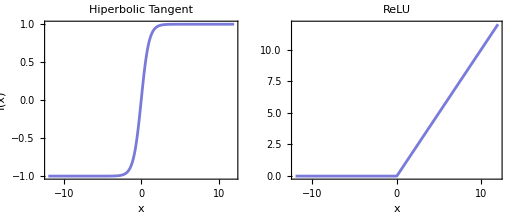

```mathematica
GraphicsRow@{Plot[tanhLayer[x,TargetDevice->"CPU"],{x,-12,12},PlotLabel->"Hiperbolic Tangent",AxesLabel->{Style["x",Bold,12],Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True],
Plot[rampLayer[x,TargetDevice->"CPU"],{x,-12,12},PlotLabel->"ReLU",AxesLabel->{None,Style["f(x)",Italic]},FrameLabel->{{None,None},{Style["x",Bold,12],None}},PlotStyle->ColorData[97,25],Frame->True]}
```

Other functions can be used by their name or Wolfram Language syntax—for
instance, the SoftPlus function.

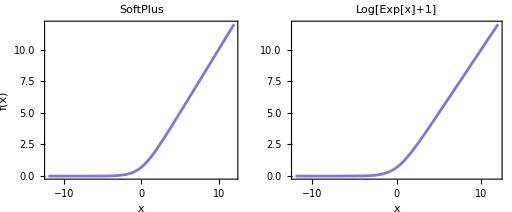

```mathematica
GraphicsRow@{Plot[ElementwiseLayer["SoftPlus"][x,TargetDevice->"CPU"],{x,-12,12},PlotLabel->"SoftPlus",AxesLabel->{Style["x",Bold,12],Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True],
Plot[Log[Exp[x]+1],{x,-12,12},PlotLabel->"Log[Exp[x]+1]",AxesLabel->{None,Style["f(x)",Italic]},FrameLabel->{{None,None},{Style["x",Bold,12],None}},PlotStyle->ColorData[97,25],Frame->True]}
```

Other standard functions are shown in the next plots, such as the scaled exponential
linear unit, sigmoid, hard sigmoid, and hard hyperbolic tangent. To view the functions supported, visit the documentation and type ElementwiseLayer in the
search box.

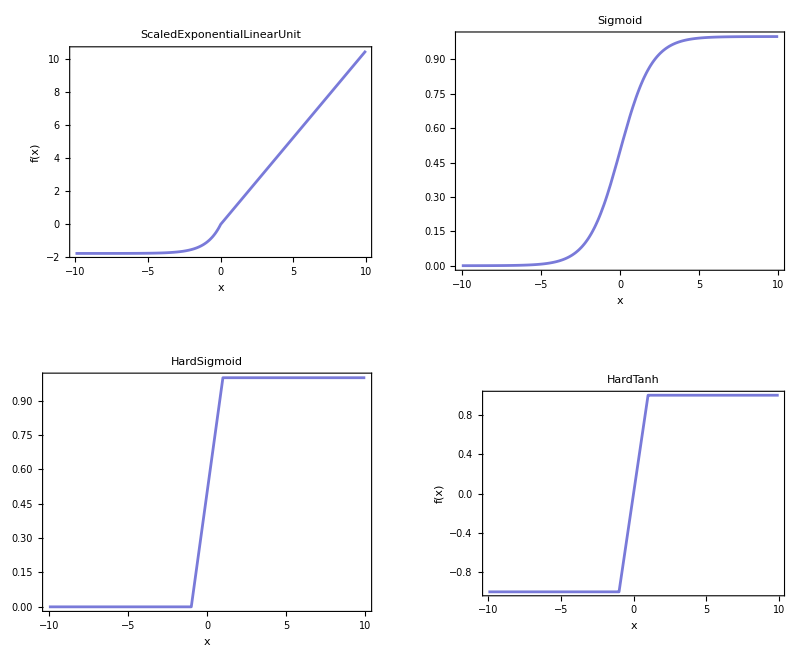

```mathematica
GraphicsGrid@Partition[Table[If[Or[activation=="Sigmoid",activation=="HardSigmoid"],Plot[ElementwiseLayer[activation][x,TargetDevice->"CPU"],{x,-10,10},FrameLabel->{Style["x",Bold],None},AxesLabel->{None,Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True,PlotLabel->activation],
Plot[ElementwiseLayer[activation][x,TargetDevice->"CPU"],{x,-10,10},AxesLabel->{Style["x",Bold],Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True,PlotLabel->activation]],{activation,{"ScaledExponentialLinearUnit","Sigmoid","HardSigmoid","HardTanh"}}],2]
```

#### Softmax Layer

SoftmaxLayer is a layer that uses the expression S(x_i)=(Exp(x_i))/(∑_(j=1)^n Exp(x_j)), where x represents a vector and x_i the components of the vector. This expression is known as the Softmax
function. The functionality of this layer consists of converting a vector to a normalized
vector, which consists of values in the range of 0 to 1. This layer is generally used to
represent a partition of the classes based on the probabilities of each one, and it is used
for tasks that involve classification. The input and output forms in the SoftmaxLayer can be entered as the other common layers except for the shape of “Real.”

```mathematica
sFL=SoftmaxLayer["Input"->4,"Output"->4];
```

Now, the layer can be applied to data.

```mathematica
SetAccuracy[sFL[{9,8,7,6}],3]
```

{0.64,0.24,0.09,0.03}

The total of the latter equals 1. SoftmaxLayer allows you to specify the level depth
of normalization, which is seen in the parameter’s properties of the layer. A level
of –1 produces the normalization of a flattened list. Also, SoftmaxLayer can receive
multidimensional arrays, not just flattened lists.

```mathematica
SoftmaxLayer[1,"Input"->{3,2}];
SetPrecision[%[{{7,8},{8,7},{7,8}}],3]//MatrixForm
```

(0.212 | 0.422
0.576 | 0.155
0.212 | 0.422)

Summing the elements of the first columns gives the same for the second column.
Another practical layer is called CrossEntropyLossLayer. This layer is widely used as a
loss function for classification tasks. This loss layer measures how well the classification
model performs. Entering the string Probabilities as an argument of the loss layer
computes the cross-entropy loss by comparing the input class probability to the target
class probability.

```mathematica
CrossEntropyLossLayer["Probabilities","Input"->3];
```

Now, the target form is set to the probabilities of the classes; the inputs and targets
are entered the same way as with MeansSquaredLoss.

```mathematica
%[<|"Input"->{0.2,0.5,0.3},"Target"->{0.3,0.5,0.2}|>]
```

1.0702

Setting the Binary argument in the layer is used when the probabilities constitute a
binary alternative.

```mathematica
CrossEntropyLossLayer["Binary","Input"->1];
%[<|"Input"->0.1,"Target"->0.9|>]
```

2.08286

To summarize the properties of layers in the Wolfram Language, the inputs and
outputs of the layers are always scalars and numeric matrices. Layers are evaluated using lower number precision, such as single-precision numbers. Layers have the property of being differentiable; this helps the model to perform efficient learning since some learning methods go into convex optimization problems. The Wolfram Language has many layers, each with specific functions. To display all the layers within Mathematica, check the documentation or write ?* Layer, which gives you the commands with the word layer associated at the end. Each layer has different behaviors, operations, and parameters, although some may resemble other commands, such as Append and AppendLayer. It is important to know the different layers and what they can do to best use them.

#### Function Layer

Another recently introduced (version 12.2) and updated (version 13) layer is the
FunctionLayer. Unlike the ElementwiseLayer, this layer allows users to apply custom
functions that do not come by default in the documentation library. This makes
it a flexible tool for more complex operations, where the function to be applied is
determined by the user.

```mathematica
FunctionLayer[#*4&]
```

FunctionLayer[…]

The input and output definitions are similar to the previous layers you have seen. It
can be an arbitrary array of input with no shape specification. However, the output shape is determined based on the function used within the layer; for instance, in the previous example, the input is a scalar (represented as a one-element array) and returns a scalar.

```mathematica
FunctionLayer[1/(1+Exp[-#])&];
%[{2,-3,4}]
```

{0.880797,0.0474259,0.982014}

With FunctionLayer, built-in functions can also be used instead of user-defined
functions, for instance, the logistic sigmoid function, which returns the same as the
latter code.

```mathematica
FunctionLayer[LogisticSigmoid];
%[{2,-3,4}]
```

{0.880797,0.0474259,0.982014}

A difference between FunctionLayer and ElemewiseLayer is that you can apply a
function to each element independently in the first. On the other hand, it performs
element-wise operations, ensuring shape consistency.

### Encoder and Decoders

Suppose audio, images, or other types of variables are intended to be used. In that case, this type of data needs to be converted into a numeric array to be introduced as input into a layer. This is where encoders and decoders come into play.

#### Encoder

Layers must have a NetEncoder attached to the input to perform a correct construction. The NetEncoders interpret the image, audio, and data to a numeric value to be used inside a net model. Different names are associated with the encoding type. The most common are Boolean (True or False, encoding as 1 or 0), Characters (string characters as one-hot vector encoding), Class (class labels as integer encoding), Function (custom function encoding), Image (2D image encoding as a rank 3 array), and Image3D (3D image encoding as a rank 4 array). The arguments of the encoder are the name or the name and the corresponding features of the encoder.

```mathematica
NetEncoder["Boolean"]
```

NetEncoder[…]

To test the encoder, you use the following.

```mathematica
Print["Booleans: ",{%[True],%[False]}]
```

Booleans: {1,0}

A NetEncoder can have classes with different index labels. Like a classification of
class X and class Y, this corresponds to an index of the range from 1 to 2.

```mathematica
NetEncoder[{"Class",{"Class X","Class Y"}}]
```

NetEncoder[…]

```mathematica
Print["Classes: ",%[Table[RandomChoice[{"Class X","Class Y"}],{i,10}]]]
```

Classes: {2,2,1,2,1,1,2,2,1,2}

The following is used for a unit vector.

```mathematica
NetEncoder[{"Class",{"Class X","Class Y","Class Z"},"UnitVector"}];
Print["Unit Vector: ",%[Table[RandomChoice[{"Class X","Class Y","Class Z"}],{i,5}]]]
Print["MatrixForm: ",%%[Table[RandomChoice[{"Class X","Class Y","Class Z"}],{i,5}]]//MatrixForm[#]&]
```

Unit Vector: {{0,0,1},{0,0,1},{0,1,0},{0,0,1},{0,1,0}}

MatrixForm: (1 | 0 | 0
0 | 0 | 1
1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Depending on the name used inside NetEncoder, properties related to the encoder
may vary. This is depicted in the different encoder objects that are created. To attach a NetEncoder to a layer, the encoders are entered at the input port—for example, for an ElementwiseLayer. In this case, the input port of the layer has the name Boolean; the layer recognizes that this is a NetEncoder of a Boolean type. Clicking the name Boolean shows the relevant properties.

```mathematica
ElementwiseLayer[Sin,"Input"->NetEncoder["Boolean"]]
```

ElementwiseLayer[…]

For a LinearLayer, use the following form.

```mathematica
LinearLayer["Input"->NetEncoder[{"Class",{"Class X","Class Y"}}],"Output"->"Scalar"]
```

LinearLayer[…]

A NetEncoder is also used to convert images into numeric matrices or arrays by
specifying the class, the size or width, and height of the output dimensions, and the color space, which can be grayscale, RGB, CMYK, or HSB (hue, saturation, and brightness); for example, encoding an image that produces a 1×28×28 array in grayscale, or 3×28×28 array in an RGB scale, no matter the size of the input image. The first rank of the array represents the color channel, and the other two represent the spatial dimensions.

```mathematica
Table[NetEncoder[{"Image",{28,28},"ColorSpace"->Color}],{Color,{"Grayscale","RGB"}}]
```

{NetEncoder[…],NetEncoder[…]}

Once the encoder has been established, it can be applied to the desired image; then,
the encoder creates a numeric matrix with the specified size. Creating a NetEncoder
for an image shows relevant properties such as type, input image size, and color space,
among others. Applying the encoder generates a matrix in the size previously established.

```mathematica
imgEncoder=NetEncoder[{"Image",{3,3},"ColorSpace"->"CMYK"}];
Print["Numeric Matrix: ",SetPrecision[%[ExampleData[{"TestImage","House"}]],3]//MatrixForm]
```

Numeric Matrix: ((0.255
0.169
0.255) | (0.145
0.00392
0.0235) | (0.0784
0.0118
0.0275)
(0.153
0.196
0.129) | (0.2
0.31
0.255) | (0.259
0.349
0.306)
(0.0471
0.102
0.00784) | (0.165
0.322
0.165) | (0.263
0.384
0.176)
(0.161
0.263
0.184) | (0.255
0.408
0.478) | (0.325
0.388
0.569))

The output generated is a numeric matrix that is now ready to be implemented in
a network model. If the input image shape is in a different color space, the encoder
reshapes and transforms the image into the established color space. The image used in
this example is obtained from the ExampleData[{“TestImage,” “House”}].

#### Pooling Layer

Encoders can be added to the ports of single layers or containers by specifying the
encoder to the port—for instance, a PoolingLayer. These layers are used primarily on
convolutional neural networks.

```mathematica
poolLayer=PoolingLayer[{3,3},{2,2},PaddingSize->0,"Function"->Max,"Input"->NetEncoder[{"Image",{3,3},"ColorSpace"->"CMYK"}]]
```

PoolingLayer[…]

or directly use imgEncoder variable:

```mathematica
poolLayer=PoolingLayer[{3,3},{2,2},PaddingSize->0,"Function"->Max,"Input"->imgEncoder]
```

PoolingLayer[…]

The latter layer has a specification for a two-dimensional PoolingLayer with a
kernel size of 3×3 and a stride of 2×2, which is the step size between kernel applications. PaddingSize adds elements at the beginning and the end of the input matrix. This is done so that the division between the matrix and kernel sizes is an integer, preventing the loss of information between layers. Function indicates the pooling operation function, which is Max; this calculates the maximum value in each filter patch. It can also compute the mean and total for the average and summation of the filter values, respectively. Sometimes, they might be known as max, average, and sum pooling layers.

```mathematica
SetPrecision[poolLayer[ExampleData[{"TestImage","House"}]],3]//MatrixForm
```

((0.255)
(0.349)
(0.384)
(0.569))

#### Decoders

Once the net operations are finished, it return numeric expressions. On the other hand, in some tasks, you do not want numeric expressions, such as in classification tasks where classes can be given as outputs, where the model can tell that a particular object belongs to a class A and another object belongs to a class B, so a vector or numeric array can represent a probability of each class. To convert the numeric arrays into other forms of data, a NetDecoder is used.

```mathematica
decoder=NetDecoder[{"Class",CharacterRange["W","Z"]}]
```

NetDecoder[…]

The dimension of the decoder is equal to class construction. You can apply a vector
of probabilities, and the decoder interprets it and tells you the class to which it belongs. It also displays the probabilities of the classes.

```mathematica
decoder@{0.3,0.2,0.1,0.4}
```

Z

TopDecisions, TopProbabilites, and uncertainty of the probability distribution are
displayed as follows.

```mathematica
TableForm[{decoder[{0.3,0.2,0.1,0.4},"TopDecisions"->4],
decoder[{0.3,0.2,0.1,0.4},"TopProbabilities"->4],
decoder[{0.3,0.2,0.1,0.4},"Entropy"]},
TableDirections->Column,TableHeadings->{{Style["TopDecisions",Italic],Style["TopProbabilities",Italic],Style["Entropy",Italic]},None}]
```

TopDecisions | Z | W | X | Y
TopProbabilities | Z→0.4 | W→0.3 | X→0.2 | Y→0.1
Entropy | 1.27985 |  |  |

Given the list of values, input depth is added to define the class’s application level.

```mathematica
NetDecoder[{"Class",CharacterRange["X","Z"],"InputDepth"->2}];
```

Applying the decoder to a nested list of values produces the following.

```mathematica
TableForm[{%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"TopDecisions"->3],
%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"TopProbabilities"->3],
%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"Entropy"]},
TableDirections->Column,TableHeadings->{{Style["TopDecisions",Italic],Style["TopProbabilities",Italic],Style["Entropy",Italic]},None}]
```

TopDecisions | Z
Y
X | Y
X
Z
TopProbabilities | Z→0.6
Y→0.3
X→0.1 | Y→0.4
X→0.3
Z→0.3
Entropy | 0.897946 | 1.0889

A decoder is added to the output port of a layer, container, or network model.

```mathematica
SoftmaxLayer["Output"->NetDecoder[{"Class",{"X","Y","Z"}}]];
```

Applying the layer to the data produce the probabilities for each class.

```mathematica
{%@{1,3,5},%[{1,3,5},"Probabilities"],%[{1,3,5},"Decision"]}
```

{Z,<|X→0.0158762,Y→0.11731,Z→0.866813|>,Z}

#### Applying Encoder and Decoders

You are ready to implement the whole process of encoding and decoding. First, the image is resized by 200 pixels in width to show how the original image looks before encoding.

```mathematica
img=ImageResize[ExampleData[{"TestImage","House"}],200]
```

-Graphics-

```mathematica
encoder=NetEncoder[{"Image",{100,100},"ColorSpace"->"RGB"}];
decoder=NetDecoder[{"Image",ColorSpace->"Grayscale"}];
```

Then, the encoder is applied to the image, and the decoder is applied to the numeric matrix. The dimensions of the decoded image are checked to see if they match the
encoder output dimensions.

```mathematica
encoder[img];
decoder[%]
```

-Graphics-

It shows that the image has been converted into a grayscale image with new dimensions.

```mathematica
ImageDimensions[%]
```

{100,100}

As seen, the picture has been resized. Try to look at the steps in the process, like
viewing the numeric matrix and the objects corresponding to the encoder and decoder. Using the encoders and decoders involves the data type you use because every net model receives different inputs and generates different outputs.

### NetChains and Graphs

Neural networks consist of different layers, not individual layers on their own. The
NetChain command or the NetGraph command is used to construct more complex
structures with more than one layer.

#### Containers

Containers are valuable for properly operating and constructing neural networks in the Wolfram Language. In the Wolfram Language, containers are structures that assemble the infrastructure of the neural network model. Containers can have multiple forms. NetChain is useful for creating linear and non-linear structures’ nets. This helps the model to learn non-linear patterns. You can think that each layer in a network has a level of abstraction that detects complex behavior, which could not be recognized if you only worked with one single layer. As a result, you can build networks in a general way, starting from three layers: the input layer, the hidden layer, and the output layer. When there are more than two hidden layers, it is deep learning; for more information, refer to Introduction to Deep Learning: From Logical Calculus to Artificial Intelligence by Sandro Skansi (Springer, 2018).

NetChain can join two operations. They can be written as a pure function instead of
just the function’s name.

```mathematica
NetChain[{ElementwiseLayer[LogisticSigmoid@#&],ElementwiseLayer[Sin@#&]}]
```

NetChain[…]

The object returned is a NetChain, and the icon of three colored rectangles appears.
This means that the object created (NetChain) or referred to is a net chain and contains layers. If the chain is examined, it shows the input, first (LogisticSigmoid), second (Sin), and output layers. The operations are in order of appearance, so the first layer is applied and then the second. The input and output options of other layers are supported in NetChain, such as a single real number (Real), an integer (Integer), an “n”-length vector, and a multidimensional array.

```mathematica
NetInitialize@NetChain[{3,4,12,Tanh},"Input"->1]
```

NetChain[…]

NetChain recognizes the Wolfram Language function names and associates them with their corresponding layers, like 3, 4, and 12. They represent a linear layer with outputs of sizes 3, 4, and 12 (see Figure 9-28). The Tanh function represents the elementwise layer.

Let’s append a layer to the chain created with NetAppend or NetPrepend. Many of the original commands of the Wolfram Language have the same meaning—for example, to delete in a chain would be NetDelete[net_ name, #_of_layer].

```mathematica
NetInitialize@NetChain[{1,ElementwiseLayer[LogisticSigmoid@#&]},"Input"->1];
netCH2=NetInitialize@NetAppend[%,{1,ElementwiseLayer[Cos[#]&]}]
```

NetChain[…]

Different options are available when a net is applied to data, such as NetEvaluationMode (mode of evaluation, either train or test), TargetDevice, and
WorkingPrecision (numeric precision).

```mathematica
netCH2[{{0},{2},{44}},NetEvaluationMode->"Train",TargetDevice->"CPU",WorkingPrecision->"Real64",RandomSeeding->8888]
```

{{0.967873},{0.990894},{1.}}

Another form is to enter the explicit names of layers in a chain, which is typed as an
association.

```mathematica
NetInitialize@NetChain[<|"Linear Layer 1"->LinearLayer[3],"Ramp"->Ramp,"Linear Layer 2"->LinearLayer[4],"Logistic"->ElementwiseLayer[LogisticSigmoid]|>,"Input"->3]
```

NetChain[…]

Inspecting the layer’s contents should appear after clicking the layer’s name or the layer. If a layer wants to be extracted, then NetExtract is used along with the name of
the corresponding layer. The output is suppressed, but the layer should pop out if the
semicolon is removed.

```mathematica
NetExtract[%,"Logistic"];
```

To extract all of the layers in one line of code, Normal does the job.

```mathematica
Normal[netCH2]//Column
```

LinearLayer[…]
ElementwiseLayer[…]
LinearLayer[…]
ElementwiseLayer[…]

#### Multiple Chains

Chains can be joined with a nested chain.

```mathematica
chain1=NetChain[{12,SoftmaxLayer[]}];
chain2=NetChain[{1,ElementwiseLayer[Cos[#]&]}];
nestedChain=NetInitialize@NetChain[{chain1,chain2},"Input"->12]
```

NetChain[…]

This chain is divided into two NetChains, each representing a chain. In this case, you
see chain1 and chain2, and each chain shows its corresponding nodes. To flatten the
chains, use NetFlatten.

```mathematica
NetFlatten[nestedChain]
```

NetChain[…]

#### NetGraphs

The NetChain command only joins layers in which the output of a layer is connected
to the input of the next layer. NetChain does not work in connecting inputs or outputs
to other layers; it only works with one layer. To work around this, the use of NetGraph is required. Besides allowing more inputs and layers, NetGraph represents the neural network’s structure and process with a graph.

```mathematica
NetInitialize@NetGraph[{LinearLayer["Output"->1,"Input"->1],Cos,SummationLayer[]},{}]
```

NetGraph[…]

The object crafted is a NetGraph, represented by the figure of the connecting
squares. The input goes to three different layers, each with its output. NetGraph accepts two arguments: the first is for the layers or chains, and the second is to define the graph vertices or connectivity of the net. For example, the net has three outputs in the latter code because the vertices were not specified. SummationLayer is a layer that sums all the input data.

```mathematica
net1=NetInitialize@NetGraph[{LinearLayer["Output"->2,"Input"->1],Cos,SummationLayer[]},{1->2->3}]
```

NetGraph[…]

The vertex notation means that the output of a layer is given to another layer, and so
on. In other words, 1 → 2 → 3 means that the output of the linear layer is passed to the
next layer until it is finally summed up in the last layer with the summation layer, thus preserving the order of appearance of the layers. However, you can alter the order of each vertex. The net can be modified so that outputs can go to other layers of the net, such as 1 to 3 and then to 2. With NetGraph, layers and chains can be entered as a list or an association. The vertices are typed as a list of rules.

```mathematica
net2=NetInitialize@NetGraph[{LinearLayer["Output"->2,"Input"->1],Cos,SummationLayer[]},{1->3->2}]
```

NetGraph[…]

The inputs and outputs of each layer are marked by a tooltip that appears when
passing the cursor over the graph lines or vertices. Because input and output are not
specified, NetGraph infers the data type in the input and output port; this is the case for the capital R in the input and output of the layer used, which stands for real.

With NetGraph, layers can be entered as a list or association. The connections are
typed as a list of rules.

```mathematica
NetInitialize@NetGraph[<|"Layer 1"->LinearLayer[2,"Input"->1],"Layer 2"->Cos,"Layer 3"->SummationLayer[]|>,{"Layer 2"->"Layer 1"->"Layer 3"}]
```

NetGraph[…]

It is possible to specify how many inputs and outputs a structure can have from the
NetPort command.

```mathematica
NetInitialize@NetGraph[{LinearLayer[3,"Input"->1],LinearLayer[3,"Input"->2],LinearLayer[3,"Input"->1],TotalLayer[]},{NetPort["1st Input"]->1,NetPort["2nd Input"]->2,NetPort["3rd Input"]->3,{1,2,3}->4}]
```

NetGraph[…]

If you have more than one input, each input is entered in the specified port.

```mathematica
%[<|"1st Input"->32.32,"2nd Input"->{2,π},"3rd Input"->1|>]
```

{82.4758,-42.202,-37.4852}

If having more than one output, the results are displayed for every different output.

```mathematica
NetInitialize[NetGraph[{LinearLayer[1,"Input"->1],LinearLayer[1,"Input"->1],LinearLayer[1,"Input"->1],Ramp,ElementwiseLayer["ExponentialLinearUnit"],LogisticSigmoid},{1->4->NetPort["Output1"],2->5->NetPort["Output2"],3->6->NetPort["Output3"]}],RandomSeeding->8888]
%[{1}]
```

NetGraph[…]

<|Output1→{0.},Output2→{-0.289052},Output3→{0.860635}|>

NetChain containers can be treated as layers with NetGraph. Some layers, such as the CatenateLayer, accept zero arguments.

```mathematica
NetInitialize@NetGraph[{LinearLayer[1,"Input"->1],NetChain[{LinearLayer[1,"Input"->1],ElementwiseLayer[LogisticSigmoid[#]&]}],NetChain[{LinearLayer[1,"Input"->1],Ramp}],ElementwiseLayer["ExponentialLinearUnit"],CatenateLayer[]},{1->4,2->5,3->5,4->5}]
```

NetGraph[…]

Clicking the chain or the layer shows the relevant information, and clicking the layer
inside a chain gives the information about the layer on the selected chain.

#### Combining Containers

NetChains, and NetGraphs can be nested to form different structures, as seen in the
following example, where a NetGraph and vice versa can follow a NetChain.

```mathematica
n1=NetGraph[{1,Ramp,2,LogisticSigmoid},{1->2,2->3,3->4}];
n2=NetChain[{3,SummationLayer[]}];
NetInitialize@NetGraph[{n2,n1},{2->1},"Input"->22]
```

NetGraph[…]

From the graph, it is clear that the input goes to the NetGraph, and the output of the NetGraph goes to the NetChain. A NetChain or NetGraph that has not been initialized appears in red. A fundamental quality of the containers (NetChain, NetGraph) is that they can behave as a layer. With this in mind, you can create nested containers involving only NetChains, NetGraphs, or both.

Just as a demonstration, more complex structures can be created with NetGraph, like
the following. Once a network structure is created, properties about every layer or chain can be extracted. For instance, with SummaryGraphic, you can obtain the graphic of the network graph.

```mathematica
net=NetInitialize@NetGraph[{LinearLayer[10],Ramp,10,SoftmaxLayer[],TotalLayer[],ThreadingLayer[Times]},{1->2->3->4,{1,2,3}->5,{1,5}->6},"Input"->"Real"];
Information[net,"SummaryGraphic"]
```

-Graphics-

#### Network Properties

The properties related to the numeric arrays of the network are Arrays (gives each array in the network), ArraysCount (the number of arrays in the net), ArraysDimensions (dimensions of each array in the net), and ArraysPositionList (position of each array in the net)

```mathematica
{Dataset@Information[net,"Arrays"],Dataset@Information[net,"ArraysDimensions"],Dataset@Information[net,"ArraysPositionList"]}
```

{,,}

Information related to the variable type in the input and output ports are shown with
InputPorts and OutputPorts.

```mathematica
{Information[net,"InputPorts"],Information[net,"OutputPorts"]}
```

{<|Input→Real|>,<|Output1→10,Output2→10|>}

You can see that the input is a real number, and the net has two output vectors of
size 10. The most used properties related to layers are Layers (returns every layer of
the net), LayerTypeCounts (number of occurrences of a layer in the net), LayersCount
(number of layers in the net), LayersList (a list of all the layers in the net), and LayerTypeCounts (number of occurrences of a layer in the net). The following shows for Layers and LayerTypeCounts.

```mathematica
Dataset@{Information[net,"Layers"],Information[net,"LayerTypeCounts"]}
```

Visualization of the net structure is achieved with the properties LayersGraph (a graph showing the connectivity of the layers), SummaryGraphics (graphic of the net structure), MXNetNodeGraph (MXNeT raw graph operations), and MXNetNodeGraphPlot (annotated graph of MXNet operations). MXNet is an open-
source deep learning framework that supports a variety of programming languages,
and one of them is the Wolfram Language. In addition, the Wolfram Neural Network
Framework works with MXNet structure as backend support.

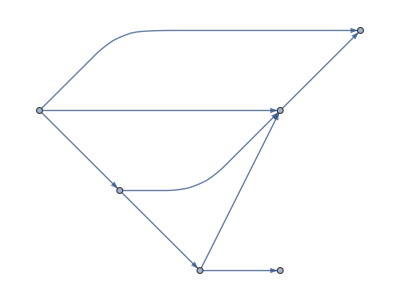
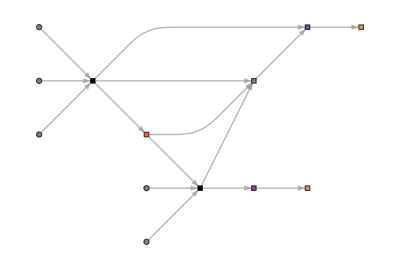
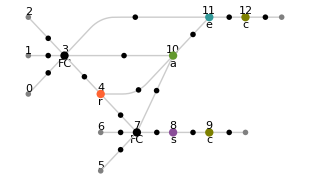
Layers Connection | NetGraph
-Graphics- | -Graphics-
MXNet Layer Graph | MXNet Ops Graph
-Graphics- | -Graphics-

```mathematica
Grid[{{Style["Layers Connection",Italic,20,ColorData[105,4]],Style["NetGraph",Italic,20,ColorData[105,4]]},{Information[net,"LayersGraph"],Information[net,"SummaryGraphic"]},{Style["MXNet Layer Graph",Italic,20,ColorData[105,4]],Style["MXNet Ops Graph",Italic,20,ColorData[105,4]]},{Information[net,"MXNetNodeGraph"],Information[net,"MXNetNodeGraphPlot"]}},Dividers->All,Background->{{{None,None}},{{Opacity[1,Gray],None}}}]
```

Passing the cursor pointer over a layer or node in the MXNet symbol graph, a tooltip
shows the properties of the MXNet symbols like ID, name, parameters, attributes,
and inputs.

#### Exporting and Importing a Model

Because of the interoperability of the Wolfram Language and MXNet, the Wolfram
Language supports the import and export of neural nets, initialized or uninitialized. You create a folder on the desktop with the MXNet Nets name and export the network found in the Net variable.

```mathematica
fileDirectory="~/Desktop";
Export[FileNameJoin[{fileDirectory,"MxNet.json"}],net,"MXNet","ArrayPath"->Automatic,"SaveArrays"->True]
```

~/Desktop/MxNet.json

Exporting the network to the MXNet format generates two files: a JSON file that
stores the topology of the neural network and a file of type .params that contains
the required parameters (numeric arrays used in the network) data for the exported
architecture; once it has been initialized. With ArrayPath set to Automatic, the params file is saved in the same net folder. Otherwise, it can have a different path. SaveArrays indicate whether the numeric arrays are exported (True) or not (False). Let’s check the two files created in the MXNets Nets folder.

```mathematica
FileNames[All,File@fileDirectory]
```

{~/Desktop/MxNet.json,~/Desktop/MxNet.params}

To import an MXNet network, the JSON and params files are recommended to be
in the same folder because the Wolfram Language assumes that a certain JSON file
matches the pattern of the params file. There are various ways to import a net, including Import[file_name.json, “MXNet”] and Import[file_name.json,{“MXNet,” element}] (the same as with .param files). Since version 13, nets are no longer imported as net chains or net graphs but can now be imported as net external objects. However, if you don’t intend to use the neural network outside of the Wolfram Language, it’s much simpler to store it as a WLNet, which facilitates easier saving and retrieval within the Wolfram Language environment. To export the net to the WLNet format, you can use the following code: Export[“file_name.wlnet”, <net_symbol or variable_name>]. Then, you can import the net using Import[“file_name.wlnet”]

```mathematica
Import[FileNameJoin[{fileDirectory,"MxNet.json"}],{"MXNet","NetExternalObject"},InputPorts-><|"Input"->{1}|>,"ArrayPath"->None];
```

The latter net was imported with the .params file automatically. To import the net
without the parameters, use ArrayPath set to None or set the params file path. Importing the net parameters can be done with a list (ArrayList), the names (ArrayNames), or an association (ArrayAssociation)

```mathematica
Row[Dataset[Import[FileNameJoin[{fileDirectory,"MxNet.json"}],{"MXNet",#}]]&/@{"ArrayAssociation","ArrayList","ArrayNames"}]
```

The elements of the net to import are InputNames, NetExternalObject, NodeDataset
(a dataset of the nodes of the MXNet), NodeGraph (nodes graph of the MXNet),
NodeGraphPlot (plot of nodes of the MXNet). The following dataset shows a few options listed.

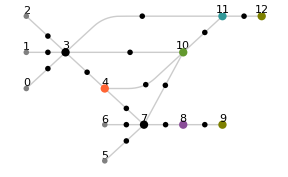

```mathematica
{Import[FileNameJoin[{fileDirectory,"MxNet.json"}],{"MXNet","NodeDataset"}],Import[FileNameJoin[{fileDirectory,"MxNet.json"}],{"MXNet","NodeGraphPlot"}]}//Row
```

Some operations between the Wolfram Language and MXNet are not reversible.
If you pay attention, the network input, exported to MXNet format, was set as a real
number, unlike the network input imported in MXNet format, which marks that the
input is an array with specifying dimensions.

When constructing a neural network, there is no restriction on how many net chains or net graphs a net can have. For instance, the following example is a neural network from the Wolfram Neural Net Repository, which has a deeper sense of construction. This net is called CapsNet, which is used to estimate the depth map of an image. To consult the net, enter NetModel[“CapsNet Trained on MNIST Data,” “DocumentationLink”] for the documentation web page; for the notebook on the Wolfram Cloud, enter NetModel[“CapsNet Trained on MNIST Data,”
“ExampleNotebookObject”] or just ExampleNotebook for the desktop version.

```mathematica
NetModel["CapsNet Trained on MNIST Data"]
```

NetGraph[<8>, <12>]

### Summary

This chapter introduced the neural network scheme in the Wolfram Language and
covered basic layers components : data input, weight, and biases . Additionally, the
chapter focuses on the encoders and decoders, explaining its structure .